Background

```mathematica
coord ={t,r,θ,ϕ};
metric=({{-(1-(2M)/r-Λ/3 r^2), 0, 0, 0}, {0, 1/(1-(2M)/r-Λ/3 r^2), 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[θ]^2}});
```

```mathematica
$Assumptions= And[t∈Reals,ω∈Reals];
metricsign=-1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<diffgeo.m
```

```mathematica
EEstep1 = RicciTensor-1/2 RicciScalar*metric  + Λ* metric;
```

```mathematica
EEstep2 = EEstep1  //FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Riemann;
```

```mathematica
contract[lower[Riemann,{4}]**lower[Riemann,{4}],{1,5},{2,6},{3,7},{4,8}]
```

(48 M^2)/r^6+(8 Λ^2)/3

Perturbation

```mathematica
Φ=1/r Exp[-ⅈ*ω*t]*Ψ[r]
```

(ⅇ^(-ⅈ t ω) Ψ[r])/r

```mathematica
SEstep1=scalarLaplacian[Φ];
SEstep2=Collect[-r*(1-(2M)/r-Λ/3 r^2)*(SEstep1/Exp[-ⅈ*ω*t]-(l(l+1))/r^3 Ψ[r]),{Ψ''[r],Ψ'[r],Ψ[r]},Simplify]
```

-r (1-(2 M)/r-(r^2 Λ)/3) (-(l (1+l))/r^3+(2 (-3 M+r^3 Λ))/(3 r^4)-(3 ω^2)/(6 M-3 r+r^3 Λ)) Ψ[r]-(2 (-3 M+r^3 Λ) (6 M-3 r+r^3 Λ) Ψ'[r])/(9 r^3)-((6 M-3 r+r^3 Λ)^2 Ψ''[r])/(9 r^2)

```mathematica
c[r_]=r (1-(2 M)/r-(r^2 Λ)/3) ((l (1+l))/r^3-(2 (-3 M+r^3 Λ))/(3 r^4)+(3 ω^2)/(6 M-3 r+r^3 Λ))//FullSimplify;
b[r_]=-(2 (-3 M+r^3 Λ) (6 M-3 r+r^3 Λ))/(9 r^3)//FullSimplify;
a[r_]=-((6 M-3 r+r^3 Λ)^2)/(9 r^2)//FullSimplify;
```

```mathematica
V[r_]=-1/(4 a[r]^2)(2b[r]*a'[r]-b[r]^2-2a[r](b'[r]-2c[r]))/.M->Sqrt[8/9]/4/.Λ->1//FullSimplify
```

(-1-6 √2 l (1+l) r+18 l (1+l) r^2+8 √2 r^3+4 r^6-6 r^4 (3+l+l^2+3 ω^2))/(2 r^2 (√2-3 r+r^3)^2)

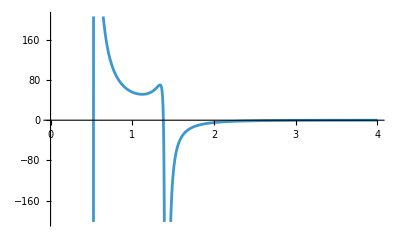

```mathematica
Plot[V[x]/.ω->0.1/.l->3,{x,0,4}]
```

```mathematica
Solve[r^3-3r+Sqrt[2]==0,r]
```

{{r→√2},{r→1/2 (-√2-√6)},{r→1/2 (-√2+√6)}}

```mathematica
N[Sqrt[2]]
N[1/2 (-√2+√6)]
```

1.41421

0.517638

```mathematica
Vevent[ϵ_]=Normal[Series[V[r],{r,1/2 (-√2+√6),0}]]/.r->ϵ+1/2 (-√2+√6)//FullSimplify;
Vevent[ϵ_]=Collect[Vevent[ϵ],ϵ]
```

(2 (-26+15 √3) (1+2 ω^2))/((-1+√3)^6 ϵ^2)-(2 √2 (45-26 √3+2 (-7+4 √3) l (1+l)+(14-8 √3) ω^2))/((-1+√3)^6 ϵ)+(-94+53 √3+(144-84 √3) l (1+l)+10 (-2+√3) ω^2)/(3 (-1+√3)^6)